# Rotations

## Equation setup

```mathematica
(* Globals:
lossEq: equation for loss
errEq: equation for error
gradEq: equation for gradient
hessEq: equation for Hessian
pre0: dummy preconditioner
n: number of layers
dsize: number of datapoints, aka f[-1]
fs: list of sizes
f[i]: gives dims, f[i],f[i-1] is dimension of layer i
W[i,j]: W[i].W[i-1]..W[j]
U[i,j]: U[i].U[i+1]...U[j]
makeW[i]: creates matrix of form {{W[i][1,1],W[i][1,2],...
Y: contains array of outputs
vars: contains all W's except W0 (same as X)
allvars: contains all W's
A[i],B[i],B[i].A[i]ᵀ define activation, backprop, gradient for layer i
Bn[i] truncated backprop for Newton's method
hessBlock[i,j] gives Hessian of layer i with respect to layer j
hess[i,j] gives Mathematica derived Hessian of layer i with respect to layer j
gradBlock[i] gives gradient at layer i
grad[i]: gives Mathematica gradient of layer i
sub1: replaces all W's and Y's with 1's
subr: replaces all W's and Y's with fixed random-looking number
*)

(* Number of features per layer *)
(* Number of layers, aka number of matmuls *)
(* f[i] shorthand for shape, W[i] has dimensions f[i]xf[i-1] *)
(* f[-1] is shorthand for dsize *)
Unprotect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];
Clear[lossEq,errEq,gradEq,hessEq,n,dsize,W,U,makeW,Y,X,vars,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];

fs={10,2,2,2};
n=Length[fs]-2;
Block[{i},For[i=1, i≤Length[fs],i++,f[i-2]=fs[[i]]]];
dsize=f[-1];

(* TODO: seal flatten/unflatten *)
Unprotect[flatten,unflatten];
flatten[Ws_]:=c2v[vec/@Ws];
unflatten[Wf_]:=Module[{flatVars,sizes},
sizes=Rest[Times@@#&/@Partition[fs,2,1]];
flatVars=listPartition[Wf,sizes];
Table[unvec[flatVars[[i]],fs[[i+2]]],{i,1,Length@sizes}]
];
Protect[flatten,unflatten];

makeW[k_]:=Array[W[k],{f[k],f[k-1]}];
vars=Table[makeW[k],{k,1,n}]; (* W1, W2, ..., Wn *)
Wf=flatten@vars;
allvars=Table[makeW[k],{k,0,n}]; (* W0, W1, W2, ..., Wn *)

Y=Array[y,{f[n],f[-1]}];
X=makeW[0];

errEq=Y-Fold[Dot,Reverse@allvars];
lossEq=1/2Tr[errEqᵀ.errEq]/dsize;
gradEq=D[lossEq,{Wf,1}];
hessEq=D[lossEq,{Wf,2}];
pre0=IdentityMatrix[Length@Wf];

(* Partial products. Shorthand notation for doing product of all layers between j and i (inclusive). W refers to original sums and U is transpose *)

(* W[i,j]=W[j].W[j-1]...W[i] *)
W[bottom_,top_]:=IdentityMatrix[f[bottom]]/;bottom<top;
W[bottom_,top_]:=Module[{sublist},
Assert[top≤bottom,"W ordering"];
sublist=allvars[[top+1;;bottom+1]];
Fold[Dot,Reverse@sublist]
];

(* U[i,j]=U[i].U[i+1]...U[j] *)
U[bottom_,top_]:=IdentityMatrix[f[top]]/;bottom>top
U[bottom_,top_]:=Module[{sublist},
Assert[bottom≤top,"U ordering"];
sublist=Transpose/@allvars[[bottom+1;;top+1]];
Fold[Dot,sublist]
];

(* Activation at layer i. Defines derivative for layer i. A[0]=Identit[dsize] *)
A[i_]:=W[i-1,0];          

(* Backprop at layer i. Defines derivative for layer i. B[n]=d_error *)
B[i_]:=-U[i+1,n].errEq/dsize;

(* Partial products needed for Newton's method *)
Bn[i_]:=U[i+1,n];

hessBlock[i_,j_]:=Module[{term1,term2},
term1=(A[i].A[j]ᵀ)⊗(Bn[i].Bn[j]ᵀ)/dsize;
Assert[Dimensions@term1=={f[i]*f[i-1],f[j]*f[j-1]}];
term2=Which[
i==j,Array[0&,Dimensions[term1]],
i<j,(A[i].B[j]ᵀ)⊗U[i+1,j-1],
i>j,U[j+1,i-1]ᵀ⊗(B[i].A[j]ᵀ)
];
(term1+term2.Kmat[f[j],f[j-1]])
];

gradBlock[i_]:=c2v@vec[B[i].A[i]ᵀ];

(* substitutes 1 to every variable *)
sub1:=Module[{},
everything=Flatten[vec/@allvars]~Join~c2v@vec@Y;
Thread[everything->Array[1&,Length@everything]]
];

(* substitutes random value to every variable *)
subr:=Module[{},
SeedRandom[0];
everything=Flatten[vec/@allvars]~Join~c2v@vec@Y;
Thread[everything->RandomReal[{-1,1},Length@everything]]
];

(* Functional versions of equations *)
errF[W_]:=errEq/.subX/.subY/.subW[W];
lossF[W_]:=lossEq/.subX/.subY/.subW[W];
gradF[W_]:=gradEq/.subX/.subY/.subW[W];
hessF[W_]:=hessEq/.subX/.subY/.subW[W];

(* Run checks *)
grad[i_]:=Module[{},Assert[i≥0 && i≤n,"grad i check"];
D[lossEq,{c2v@vec@allvars[[i+1]],1}]];

hess[i_,j_]:=Module[{},Assert[j≥0&&j≤n,"hess j check"];
D[grad[i],{c2v@vec@allvars[[j+1]],1}]];

Protect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];

idx=Range[n+1]-1; (* all valid layer indices, including W0 *)
blockIdx=Outer[List,idx,idx];

(* Checks correctness of block i,j *)
hessCheck[i_,j_]:=hess[i,j]≐hessBlock[i,j]/.subr;
gradCheck[i_]:=grad[i]==gradBlock[i]/.subr;
gradCheck/@idx
Apply[hessCheck, blockIdx,{2}]//MatrixForm
```

{True,True,True}

(True | True | True
True | True | True
True | True | True)

## Data setup

```mathematica
generateX[n_,e_,dsize_]:=Module[{wt,mean,cov,normal,X},
SeedRandom[0];
mean=Table[0,{n}];
cov=IdentityMatrix[n]*e+Array[1-e&,{n,n}];
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
centerData[X]
];
SeedRandom[0]
X0=generateX[f[0],0.01,dsize];
θ0=Pi/20;
Y0=RotationMatrix[θ0].X0;
Export["~/git/whitening/exp/data/rotations_simple_X0.csv",X0];
Export["~/git/whitening/exp/data/rotations_simple_Y0.csv",Y0];

makeInitializer[k_]:=truncatedIdentity[f[k],f[k-1]];
W0s=Table[makeInitializer[k],{k,1,n}];
W0f=flatten@W0s;
Export["~/git/whitening/exp/data/rotations_simple_W0f.csv",W0f];
Export["~/git/whitening/exp/data/rotations_simple_fs.csv",fs];

(* Todo: refactor into helper functions *)
subX:=Thread[Flatten@X->Flatten@X0];
subY:=Thread[Flatten@Y->Flatten@Y0];
subW[Wfval_]:=(Assert[Length@Wfval==Length@Wf];Thread[Wf->Wfval]);
subW0:=subW[W0f];
```

## Optimizer setup

```mathematica
(* Applies single step of optimization *)
step[x_,lr_,pre_,grad_,lossFunc_]:=Module[{},
pointList=pointList~Append~x;
gradList=gradList~Append~grad;
preList=preList~Append~pre;
lossList=lossList~Append~lossFunc[x];
x-lr*pre.grad
];
resetStep:=({pointList, gradList,preList, lossList}={{},{},{},{}};W0f);
```

## Optimizer experiments

### Gradient Descent

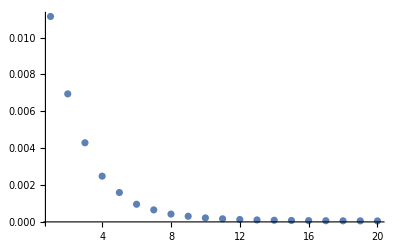

```mathematica
optimizeGradient[lr_,iters_]:=Module[{w},
w=resetStep;
For[iter=1,iter≤iters,iter++,
w=step[w,lr,pre0,gradF[w],lossF]
];
];
optimizeGradient[1.,20];
Export["~/git/whitening/exp/data/rotations_simple_gradient_losses.csv",lossList];
ListPlot[lossList,PlotRange->All]
```

```mathematica
lossList
```

{0.0111498,0.00694816,0.00429464,0.00248228,0.00159361,0.000957424,0.000651653,0.000423802,0.000306749,0.00021772,0.000167937,0.000129983,0.00010703,0.0000895942,0.0000782797,0.0000696508,0.0000636468,0.000058967,0.0000554575,0.0000526055}

### Newton's method

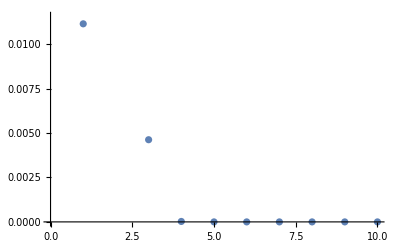

```mathematica
ihessF[W_]:=PseudoInverse@hessF@W;
optimizeNewton[lr_,iters_]:=Module[{w},
w=resetStep;
For[iter=1,iter≤iters,iter++,
w=step[w,lr,ihessF[w],gradF[w],lossF]
];
];
optimizeNewton[1.,10];
ListPlot[lossList]
```

### Newton' s method with own implementation

```mathematica
myHess0=Table[hessBlock[i,j],{i,1,n},{j,1,n}];
myhessF[W_]:=ArrayFlatten[myHess0]/.subX/.subY/.subW[W];
myihessF[W_]:=PseudoInverse[myhessf[W]];
ihessF[W0f]≐myihessF[W0f]
```

True

```mathematica
optimizeNewton2[lr_,iters_]:=Module[{w},
w=resetStep;
For[iter=1,iter≤iters,iter++,
w=step[w,lr,myihessF[w],gradF[w],lossF]
];
];
optimizeNewton2[1.,10];
ListPlot[lossList]
```

-Graphics-

## Simple Newton

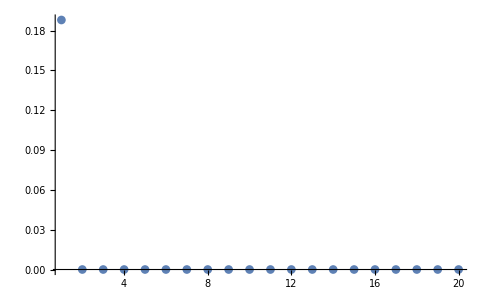

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeNewton[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*ihessf[wf].gradf[wf]
];
];
optimizeNewton[1.,W0f,20];
Export["~/git/whitening/exp/data/rotations_simple_losses_newton.csv",lossList];
ListPlot[lossList,PlotRange->All]
```

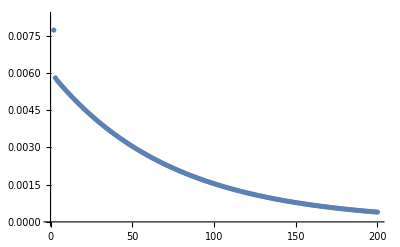

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeSGD[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf]
];
];
optimizeSGD[1.,W0f,200];
Export["~/git/whitening/exp/data/rotations_simple_losses_sgd.csv",lossList];
ListPlot[lossList]
```

## Simple2 Newton

Clear::wrsym: Symbol X is Protected.

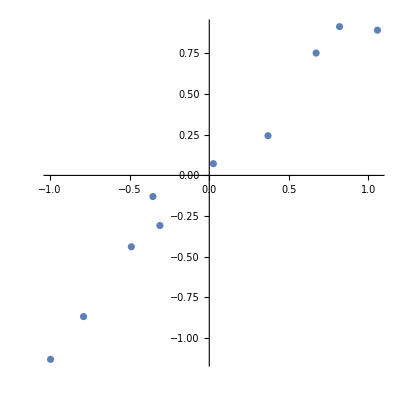

Set::wrsym: Symbol X is Protected.

```mathematica
Clear[A,B,Bn,dW,W,X,Y,y,x,fs, subW,loss,err];
fs={10,2,2,2};
Export["~/git/whitening/exp/data/rotations_simple2_fs.csv",fs];

X0=generateX[fs[[2]],0.01,fs[[1]]];
Export["~/git/whitening/exp/data/rotations_simple2_X0.csv",X0];ListPlot[Transpose@X0,AspectRatio->1]

X=Array[W[0],{fs[[2]],fs[[1]]}];
Protect[X];
subX:=(
Assert[Dimensions[X0]=={fs[[2]],fs[[1]]},"X mismatch"];Thread[Flatten@X->Flatten@X0]
);

dsize=First@fs;
n=Length[fs]-2;

makeW[k_]:=Array[W[k],{fs[[k+2]],fs[[k+1]]}];
makeInitializer[k_]:=RandomReal[{0,1},{fs[[k+2]],fs[[k+1]]}];

vars=Table[makeW[k],{k,1,n}]; (* W1, W2, ..., Wn *)
varsf=Flatten[vectorize/@vars];
Ws=vars;
Wf=varsf;
subW[Wf0_]:=Thread[Wf->Wf0];
W0=Table[makeInitializer[k],{k,1,n}];
W0f=Flatten[vectorize/@W0];


W0=Table[makeInitializer[k],{k,1,n}];
errEq:=X-Fold[Dot,Reverse@vars].X;
lossEq:=Tr[errEq.errEqᵀ]/2;

(* A[i]=W[i-1]...W[0] = fprop needed to compute derivative at layer i *)
A[Wf_,1]:=makeW[0]/.subX;
A[Wf_,i_]:=Module[{},
makeW[i-1].A[Wf,i-1]/.subW[Wf]
];

(* B[i]=W[i+1]'...d(err) = bprop needed to compute derivative at layer i *)
(* Bn[i]=W[i+1]'...Identity = partial bprop needed for Newton's method *)
err[Wf_]:=errEq/.subW[Wf]/.subX;
B[Wf_,n]:=-err[Wf];
B[Wf_,i_]:=makeW[i+1]ᵀ.B[Wf,i+1]/.subW[Wf];
Bn[Wf_,n]:=IdentityMatrix[Last@fs];
Bn[Wf_,i_]:=makeW[i+1]ᵀ.Bn[Wf,i+1]/.subW[Wf];

dW[Wf_,i_]:=-B[Wf,i].A[Wf,i]ᵀ;

(* Define loss, gradient, Hessian *)
lossf[Wf_]:=(lossEq/.subW[Wf]/.subX);
loss[Ws_]:=lossf[flatten[Ws]];

gradEq=D[lossf[Wf],{Wf,1}];
hessEq=D[lossf[Wf],{Wf,2}];
gradf[Wf_]:=gradEq/.subW[Wf];
hessf[Wf_]:=hessEq/.subW[Wf];
hessBlock[W0f_,i_]:=
D[lossf[Wf],{c2v@vectorize@Ws[[i]],2}]/.subW[W0f]

ihessf[Wf_]:=PseudoInverse[hessf[Wf]];

Assert[hessBlock[W0f,1]==(A[W0f,1].A[W0f,1]ᵀ)⊗(Bn[W0f,1].Bn[W0f,1]ᵀ),"hess check"];
Assert[hessBlock[W0f,2]==(A[W0f,2].A[W0f,2]ᵀ)⊗(Bn[W0f,2].Bn[W0f,2]ᵀ),"hess check"];


Export["~/git/whitening/exp/data/rotations_simple2_W0f.csv",W0f];
Export["~/git/whitening/exp/data/rotations_simple2_fs.csv",fs];
Export["~/git/whitening/exp/data/rotations_simple2_hess.csv",hessf[W0f]];
```

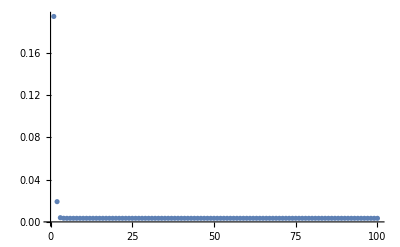

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeNewton[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*ihessf[wf].gradf[wf]
];
];
optimizeNewton[1.,W0f,100];
Export["~/git/whitening/exp/data/rotations_simple2_losses_newton.csv",lossList];
ListPlot[lossList,PlotRange->All]
```

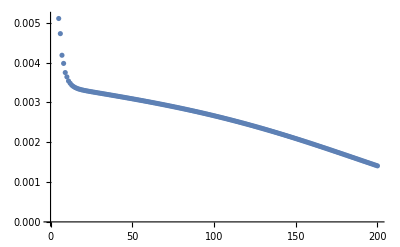

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeSGD[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf]
];
];
optimizeSGD[1.,W0f,200];
Export["~/git/whitening/exp/data/rotations_simple_losses_sgd.csv",lossList];
ListPlot[lossList]
```